## Coulomb on a infinite lattice with different spacing

```mathematica
mass=1.0;
```

```mathematica
Clear[dist];
dist[i_,j_]:=Sqrt[i^2+j^2]

Clear[g,a,b,c,latticeCoulomb];
latticeCoulomb[i_,j_,aspace_:0.1]:=1/2 NIntegrate[Cos[(x*i+y*j)]/(2.0-Cos[x]-Cos[y]+mass^2*aspace^2/2 ),{x,0,2Pi},{y,0,2Pi}]/(2Pi)^2

Clear[discretizationError];
discretizationError[i_,j_,aspace_:0.1]:=Module[{x,y},
x=N[BesselK[0,dist[i,j]]/(2Pi)];
y=latticeCoulomb[i/aspace,j/aspace,aspace];
{x,y,y-x}
]
```

### test

```mathematica
discretizationError[0,1,1]
```

{0.0670081,0.0675623,0.000554177}

```mathematica
discretizationError[0,1,0.5]
```

{0.0670081,0.0693489,0.00234079}

```mathematica
discretizationError[0,1.,0.2]
```

{0.0670081,0.0673179,0.00030981}

```mathematica
discretizationError[0,1,0.1]
```

{0.0670081,0.0670747,0.0000665903}

```mathematica
discretizationError[0,1,0.05]
```

{0.0670081,0.0670243,0.0000161356}

```mathematica
discretizationError[0,1,0.02]
```

{0.0670081,0.0670107,2.56027×10^-6}

```mathematica
discretizationError[0,1,0.01]
```

{0.0670081,0.0670088,6.39255×10^-7}

```mathematica
discretizationError[0,1,0.005]
```

{0.0670081,0.0670083,1.58647×10^-7}

```mathematica
discretizationError[0,1,0.001]
```

{0.0670081,0.0670081,6.96068×10^-9}

## Plot

```mathematica
vij={g[0,1],g[0,2],g[0,3],g[0,4],g[0,5]}/.g->latticeCoulomb
```

{0.393164,0.282903,0.220095,0.17817,0.147556}

```mathematica
rdist={g[0,1],g[0,2],g[0,3],g[0,4],g[0,5]}/.g->dist
```

{1,2,3,4,5}

```mathematica
Length[vij]==Length[rdist]
```

True

```mathematica
ord=Ordering[rdist];
rdistSorted=rdist[[ord]];
vijSorted=vij[[ord]];
```

```mathematica
data=Thread[List[rdistSorted,vijSorted]];
model=a BesselK[0,b x];
fit=FindFit[data,{model,b≥0,a>0},{a,b},x];
modelf=Function[{x},Evaluate[model/.fit]]
```

Function[{x},0.164208 BesselK[0,0.103355 x]]

```mathematica
vij2={g[1,1],g[1,2],g[2,2]}/.g->latticeCoulomb
```

{0.326062,0.260591,0.225249}

```mathematica
rdist2={g[1,1],g[1,2],g[2,2]}/.g->dist
```

{√2,√5,2 √2}

### error

```mathematica
errMax=Max[Abs[modelf[rdist]-vijSorted]]
errMax=Max[Abs[modelf[rdist2]-vij2]]
```

0.000316119

0.0114174

```mathematica
Max[Abs[BesselK[0,mass*0.1*rdist]/(2Pi)-vijSorted]]
Max[Abs[BesselK[0,mass*0.1*rdist2]/(2Pi)-vij2]]
```

0.00688383

0.00614596

```mathematica
spacing=0.1
```

0.1

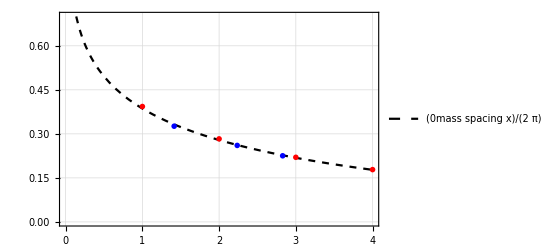

```mathematica
Show[
Plot[
BesselK[0,mass *spacing*x]/(2Pi),{x,0,4},PlotRange->{0,0.7},PlotStyle->{Black,Dashed},PlotTheme->{"Detailed"}
],
ListPlot[
{data,Thread[List[rdist2,vij2]]},PlotStyle->{{Red,PointSize[0.05]},{Blue,PointSize[0.05]}},
PlotTheme->{"Business"}
]
]
```